# CoffeeCode Interface

Set the CoffeeCode release path below (where you execute make), and the file you configured as cc-instance-custom.h during ccmake. You can use the file open dialogue helper to obtain said paths.

Note that depending on whether the build directory is set up with SYMMETRIC_SOLVER or not will NOT determine what variant of CoffeeCode is used to execute the instance; you have to do this manually.

```mathematica
SystemDialogInput["Directory"]
SystemDialogInput["FileOpen"]
```

```mathematica
CCRELEASEPATH="/home/jkrb2/programming/CoffeeCode/build/release/";
CCRELEASEPATHFULLSOLVER="/home/jkrb2/programming/CoffeeCode/build/release_full/";
CCCUSTOMINSTANCEFILE="/home/jkrb2/programming/CoffeeCode/build/release/cc-instance-custom.h";
```

```mathematica
Assert[On];(* enable sanity checks instead of failing silently *)
```

## Basic Graph Functionality [install IGraphM once below, then forget]

### IGraphM

Uncomment the last line in the following cell, then execute to install IGraphM. This only has to be done once per machine.

```mathematica
updateIGraphM[]:=Module[{json,download,target,msg},Check[json=Import["https://api.github.com/repos/szhorvat/IGraphM/releases","JSON"];
download=Lookup[First@Lookup[First[json],"assets"],"browser_download_url"];
msg="Downloading IGraph/M "<>Lookup[First[json],"tag_name"]<>" ...";
target=FileNameJoin[{CreateDirectory[],"IGraphM.paclet"}];
If[$Notebooks,PrintTemporary@Labeled[ProgressIndicator[Appearance->"Necklace"],msg,Right],Print[msg]];
URLSave[download,target],Return[$Failed]];
If[FileExistsQ[target],PacletManager`PacletInstall[target],$Failed]]
(*updateIGraphM[]*) (* uncomment this once and run to install IGraphM locally, then comment again *)
```

```mathematica
<<IGraphM`
ParallelEvaluate[<<IGraphM`;];
```

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

IGraph/M 0.3.103 (November 13, 2018)

IGraph/M 0.3.103 (November 13, 2018)

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

Evaluate IGDocumentation[] to get started.

Evaluate IGDocumentation[] to get started.

### Group for Graph State

GroupForGraph gives the full automorphism group of the underlying graph; we color the environment vertices in a different color to make sure the permutation group will be a product across this partitioning.

```mathematica
Clear[GroupForGraph]
GroupForGraph[graph_Graph,kSys_Integer]:=GroupForGraph[graph,kSys]=With[{
kEnv=VertexCount@graph-kSys
},
PermutationGroup[
PermutationCycles/@IGBlissAutomorphismGroup[{graph,"VertexColors"->ConstantArray[0,kSys]~Join~ConstantArray[1,kEnv]}]
]
]
```

### Plot Graph

```mathematica
Clear[EnvironmentPlot]
EnvironmentPlot[g_Graph,systemSize_]:=Graph[g,VertexStyle->(
Thread[(Range[VertexCount@g-systemSize]+systemSize)->Red]
),VertexSize->.2,VertexLabels->None]
```

### Create all Possible Choices of Hairs to the Environment

```mathematica
Clear[IsomorphicHairChoiceQ,HairColoring]
HairColoring[hairs_]:=HairColoring[Sort@hairs]=Length/@GroupBy[hairs,Identity]
IsomorphicHairChoiceQ[g_Graph,hairs1_,hairs2_]:=IsomorphicHairChoiceQ[g,hairs1,hairs2]=IsomorphicHairChoiceQ[g,hairs2,hairs1]=IGVF2IsomorphicQ[
{g,"VertexColors"->HairColoring@hairs1},
{g,"VertexColors"->HairColoring@hairs2}
]
IsomorphicHairChoiceQ[g_Graph]:=IsomorphicHairChoiceQ[g,#1,#2]&
```

```mathematica
Clear[HairGraph,AllHairGraphs]
HairGraph[g_,hairs_]:=HairGraph[g,hairs]=With[{
new=VertexCount@g+Range@Length@hairs
},
EdgeList[g]~Join~Thread[hairs<->new]//Graph
]
AllHairGraphs[g_,generator_:Hold[Subsets[#]⟦2;;⟧&]]:=AllHairGraphs[g,generator]=With[{
(* first check for graph isomorphism using a vertex coloring *)
uniqueHairEndpoints=DeleteDuplicates[
ReleaseHold[generator][VertexList@g],
IsomorphicHairChoiceQ[g]
]
},
HairGraph[g,#]&/@uniqueHairEndpoints
]
```

### Strong Generating Set Transversal

```mathematica
Clear[SGSTransversal]
(* the head element of the group stabilizer chain already delivers a transversal of a strong generating set *)
SGSTransversal[group_PermutationGroup]:=With[{
chain=GroupStabilizerChain[group]
},
Partition[chain,2,1]/.{Rule[sA_,gA_],Rule[sB_,gB_]}:>(
Complement[sB,sA]->PermutationGroup@Complement[GroupGenerators@gA,GroupGenerators@gB]
)
]
```

## CoffeeCode Link

### Exporting MM symbols

```mathematica
Clear[ExportAdjacencyMatrix]
ExportAdjacencyMatrix[g_Graph]:=With[{
Avec=g//AdjacencyMatrix//Normal//Flatten
},
StringJoin[ToString/@Avec]
]
```

```mathematica
Clear[SGSTransversalMMForm]
SGSTransversalMMForm[list_List,length_Integer]:=list/.{
Rule[{idx_Integer},PermutationGroup[cycles_List]]:>Module[{
permutationIndices=PermutationList[#,length]&/@cycles
},

(* the pivot point is the first index for which the SGSGenerator acts nontrivially on (so one point past the points that are stabilized).
If the pivot point for the SGSGenerator is 2, that means we want to check indices 0 and 1 in C++; in MM this would correspond to indices {1, 2}, which is what ⟦;;2⟧ truncates to.
Therefore we validly don't subtract 1 from the pivot point, but do subtract 1 from all other indices *)
StringRiffle[Flatten@{
"\tSGSGenerator<"<>ToString@(#1)<>", Group<",
("\t\tPermutation<"<>StringRiffle[ToString/@(##-1),","]<>">")&/@#2,
"\t>>"
},"\n"]&@@{idx,permutationIndices}

]
}//Flatten//("using sgs = SGSTransversal<\n"<>StringRiffle[#,",\n"]<>"\n>;")&
```

```mathematica
Clear[ExportSymmetricCCInstance]
ExportSymmetricCCInstance[graph_Graph,kSys_Integer,name_:"graphstate_instance"]:=With[{
sgs=SGSTransversal@GroupForGraph[graph,kSys],
adj=ExportAdjacencyMatrix@graph,
kTot=VertexCount@graph
},

If[Length@sgs==0,Echo["WARN: symmetry group is 0. Not a valid symmetric problem instance."]];

"struct "<>name<>" {\n"<>
SGSTransversalMMForm[sgs,kSys]<>"\n"<>
"constexpr static size_t k_sys = "<>ToString[kSys]<>", k_env = "<>ToString[kTot-kSys]<>";\n"<>
"constexpr static AdjacencyMatrixT<"<>ToString[kTot]<>"> adjacency_matrix{"<>ToString[Normal@AdjacencyMatrix@graph]<>"};\n"<>
"};"
]
```

### Build Interface

```mathematica
Clear[MakeCC]
MakeCC[kSys_Integer,kEnv_Integer]:=With[{
out=RunProcess[
{
"make",
"-B",
"K_SYS="<>ToString@kSys,
"K_ENV="<>ToString@kEnv
},
ProcessDirectory->CCRELEASEPATH
]
},
out["ExitCode"]==0
]
MakeCC[graph_Graph,kSys_Integer]:=With[{
instanceFileContent=ExportSymmetricCCInstance[graph,kSys]
},
Export[CCCUSTOMINSTANCEFILE,instanceFileContent,"Text"];
MakeCC[kSys,VertexCount@graph-kSys]
]
```

```mathematica
MakeCC[3,1]
```

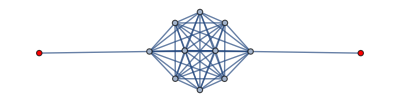
```mathematica
MakeCC[-Graphics-,10]
```

```mathematica
Clear[RunCC]
RunCC[graph_Graph,kSys_Integer]:=With[{},
If[!MakeCC[graph,kSys],Return[False]];

With[{
ccResult=RunProcess["CoffeeCode",All,ProcessDirectory->CCRELEASEPATH]
},
Assert[ccResult["ExitCode"]==0];
Assert[ccResult["StandardError"]==""];

ImportString[ccResult["StandardOutput"],"RawJSON"]
]
]
```

```mathematica
RunCC[-Graphics-,10]
```

### Full Solver Interface

```mathematica
Clear[CCPath]
CCPath[kSys_Integer,kEnv_Integer]:=CCPath[kSys,kEnv]=CCRELEASEPATHFULLSOLVER<>"CoffeeCode."<>ToString[kSys]<>"."<>ToString[kEnv]

(* RunCC overload *)
RunCC[graph_Graph,kSys_Integer,"Full"]:=Module[{
adjacencyMatrix=ExportAdjacencyMatrix@graph,
kEnv=VertexCount@graph-kSys
},
With[{
executable=Echo@CCPath[kSys,kEnv]
},

Assert[FileExistsQ[executable]];

With[{
ccResult=RunProcess[executable,All,adjacencyMatrix]
},
Assert[ccResult["ExitCode"]==0];
Assert[ccResult["StandardError"]==""];

ImportString[ccResult["StandardOutput"],"RawJSON"]
]
]
]
```

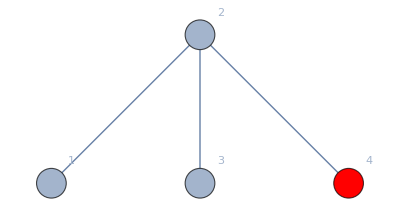
```mathematica
RunCC[-Graphics-,3,"Full"]
```

### Importing JSON format

```mathematica
Clear[MultArrayToPoly]
MultArrayToPoly[{mult_,list_}]:={
mult,
MapIndexed[f,list]/.f[coeff_,{exponent_}]:>coeff q^(exponent-1)//Total
}
```

```mathematica
Clear[PauliActionCC]
PauliActionCC[graph_Graph,kSys_Integer,p_,symmetricSolver_:True]:=Module[{
kTot=VertexCount@graph,
kEnv=VertexCount@graph-kSys,

pp={1-p,p/3,p/3,p/3},
λ,λa,λm,λma
},

Assert[kEnv≤kSys];
Assert[1≤kSys<kTot];

(* get lambda and lambda_a *)
{{λm,λ},{λma,λa}}=With[{
result=If[symmetricSolver,
RunCC[graph,kSys],
RunCC[graph,kSys,"Full"]
]
},
{
MultArrayToPoly/@result["lambda"]//Transpose,
MultArrayToPoly/@result["lambda_a"]//Transpose
}
];

(* final expression in the variables given *)
Thread/@Thread[(
p0^kSys{λ,λa/2^(kTot-kSys)}/.{
p0->pp⟦1⟧,
q->pp⟦2⟧/pp⟦1⟧
}//Simplify
)->{λm,λma}
]
]
```

```mathematica
PauliActionCC[-Graphics-,10,p]
```

## Entropy and CI

```mathematica
Clear[ShannonEntropyMult,CIMult]
ShannonEntropyMult[l_List]:=l/.Rule[0,_]:>0/.Rule[term_,mult_]:>-mult*term Log2[term]//Total
CIMult[λ_,λa_]:=(ShannonEntropyMult[λa]-ShannonEntropyMult[λ])/Log2@Total@(Last/@List@@λa)
```

## Interface

### Manual Export

#### Create graphs by hand

To create graphs by hand, look up the following functions:

```mathematica
AdjacencyGraph
SparseArray
PathGraph
```

Or directly use MM’s Graph object, where edges are entered with ESC ue ESC

```mathematica
Graph[{1<->2,3<->4,3<->5,1<->3}]
```

#### Create a random graph, add a hair, and plot.

```mathematica
CompleteGraph[10];
HairGraph[%,{10,9}];
graph=EnvironmentPlot[%,10]
```

#### Export instance

Just adjacency matrix for Full Solver

```mathematica
ExportAdjacencyMatrix[-Graphics-]
```

SGS for Symmetric Solver

```mathematica
ExportSymmetricCCInstance[graph,10]
Export[SystemDialogInput["FileSave"],%,"Text"]
```

```mathematica
ExportSymmetricCCInstance[StarGraph[9],8]
```

struct graphstate_instance {
using sgs = SGSTransversal<
	SGSGenerator<2, Group<
		Permutation<0,2,1,3,4,5,6,7>
	>>,
	SGSGenerator<3, Group<
		Permutation<0,1,3,2,4,5,6,7>
	>>,
	SGSGenerator<4, Group<
		Permutation<0,1,2,4,3,5,6,7>
	>>,
	SGSGenerator<5, Group<
		Permutation<0,1,2,3,5,4,6,7>
	>>,
	SGSGenerator<6, Group<
		Permutation<0,1,2,3,4,6,5,7>
	>>,
	SGSGenerator<7, Group<
		Permutation<0,1,2,3,4,5,7,6>
	>>
>;
constexpr static size_t k_sys = 8, k_env = 1;
constexpr static AdjacencyMatrixT<9> adjacency_matrix{{{0, 1, 1, 1, 1, 1, 1, 1, 1}, {1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0}}};
};

### Automatic Export, Build and Import

#### Get CI for a Graph

This is now a single line. Remove the semicolon to see full analytic expression.

```mathematica
CIMult@@PauliActionCC[-Graphics-,3,p];
```

For plotting, use e.g.

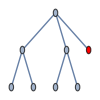
```mathematica
CIMult@@PauliActionCC[-Graphics-,7,p];
Plot[%,{p,0,1}]
```

5 Rep Code

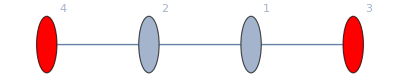
```mathematica
CIMult@@PauliActionCC[-Graphics-,2,p];
FindRoot[%,{p,.2}]
```

## Some Graph Classes

### Rooted Graph Product/Concatenated Codes

```mathematica
Clear[ConcatGraph]
ConcatGraph[g1_Graph,g2_Graph,v1_Integer,v2_Integer]:=With[{
vcount1=VertexCount@g1,
vertices2=VertexList@g2,
edges2=EdgeList@g2
},
With[{
vmap=If[#==v2,v1,If[#<v2,#+vcount1,#+vcount1-1]]&
},
GraphUnion[g1,Graph[vmap/@vertices2,Map[vmap,edges2,{2}]]]
]
]

ConcatGraph[g1_Graph,g2_Graph,v1_List,v2_Integer]:=
Fold[f,{g1,g2,v2},v1]//.f[{gg1_,gg2_,vv2_},vv1_]:>{ConcatGraph[gg1,gg2,vv1,vv2],gg2,vv2}//First
```

#### Example: 3 in 5 or some such

```mathematica
root=PathGraph[Range@5,VertexLabels->"Index"]
```

```mathematica
child=PathGraph[Range@3,VertexLabels->"Index"]
```

```mathematica
catgraph=Graph[
ConcatGraph[root,child,Range@5,2],
VertexLabels->"Index"
]
```

```mathematica
EnvironmentPlot[HairGraph[catgraph,{5}],15]
(* UNCOMMENT False HERE TO ENABLE FULL SOLVER, see comment below *)
CIMult@@PauliActionCC[%,15,p(* , False *)];
Plot[%,{p,0,1}]
FindRoot[%%,{p,.2}]
```

As a remark: while this works, using a path graph as root is terrible as it has a vanishing symmetry group. We should use something more symmetric! However, this is within the realm of the full solver, as the following shows.
Note that this is because the group order isn’t very large indeed:

```mathematica
GroupOrder@GroupForGraph[catgraph,15]
```

To estimate the number of tuples that the symmetric solver has to iterate over, we can take the estimate 4^kSys/group orbit

```mathematica
4^15/64
```

#### Better example: 4 in 5 ish

```mathematica
root=KaryTree[4,3,VertexLabels->"Index"]
```

```mathematica
child=KaryTree[4,3,VertexLabels->"Index"]
```

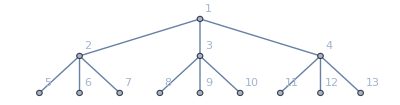

13

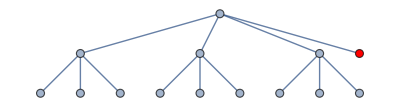

```mathematica
catgraph=Graph[
ConcatGraph[root,child,{2,3,4},1],
VertexLabels->"Index"
]
catgraphWithHair=EnvironmentPlot[HairGraph[catgraph,{1}],Echo@VertexCount@catgraph]
```

```mathematica
(* this code is significantly larger, but should be easier to compute *)
GroupOrder@GroupForGraph[catgraphWithHair,VertexCount@catgraph]
4^(VertexCount@catgraph)/%//N
```

```mathematica
CIMult@@PauliActionCC[catgraphWithHair,VertexCount@catgraph,p]//AbsoluteTiming;
First@%//Echo;

Last@%%;
Plot[%,{p,0,1}]
FindRoot[%%,{p,.2}]
```

### Let’s try a Bistar Code

```mathematica
Clear[BistarCode]
BistarCode[l1_,l2_]:=GraphUnion[
StarGraph[l1+1],
List@@@EdgeList@StarGraph[l2+1]+l1//Graph,
VertexLabels->"Index"
]
```

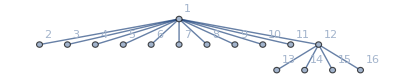

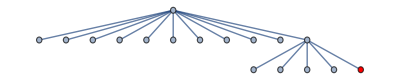

87091200

14.3429

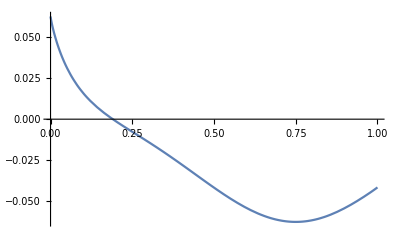

{p→0.190353}

```mathematica
With[{
A=11,
B=4
},
Module[{
g=BistarCode[A,B]//Echo,
kSys
},
kSys=VertexCount[g];

g=EnvironmentPlot[HairGraph[g,{A+1}],kSys]//Echo;
GroupOrder@GroupForGraph[g,kSys]//Echo;

CIMult@@PauliActionCC[g,kSys,p]//AbsoluteTiming
]
];

First@%//Echo;

Last@%%;
Plot[%,{p,0,1}]
FindRoot[%%,{p,.2}]
```

```mathematica
GroupForGraph[-Graphics-,16]
GroupOrbits[%]
```

PermutationGroup[{Cycles[{{15,16}}],Cycles[{{14,15}}],Cycles[{{13,14}}],Cycles[{{10,11}}],Cycles[{{9,10}}],Cycles[{{8,9}}],Cycles[{{7,8}}],Cycles[{{6,7}}],Cycles[{{5,6}}],Cycles[{{4,5}}],Cycles[{{3,4}}],Cycles[{{2,3}}]}]

{{1},{2,3,4,5,6,7,8,9,10,11},{12},{13,14,15,16}}

```mathematica
GroupForGraph[-Graphics-,13]
GroupOrbits[%]
```

PermutationGroup[{Cycles[{{6,7}}],Cycles[{{9,10}}],Cycles[{{12,13}}],Cycles[{{11,12}}],Cycles[{{8,9}}],Cycles[{{3,4},{8,11},{9,12},{10,13}}],Cycles[{{5,6}}],Cycles[{{2,3},{5,8},{6,9},{7,10}}]}]

{{1},{2,3,4},{5,6,7,8,9,10,11,12,13}}